{m[1][0]==-2.54783,x[1][0]==8.89582,m[2][0]==-3.10685,x[2][0]==0.225958}

{{0.219,0.16}}

{{0.219}}

{{0.219}}

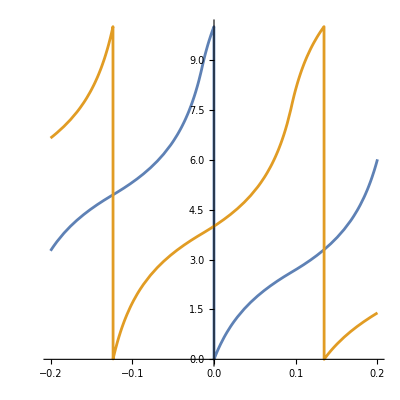

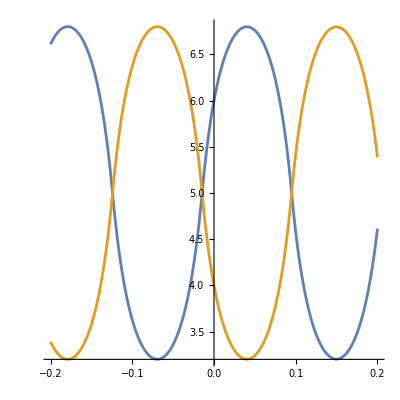

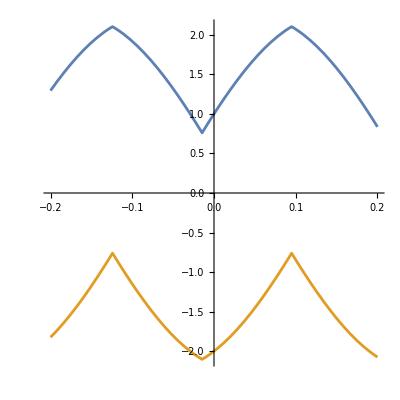

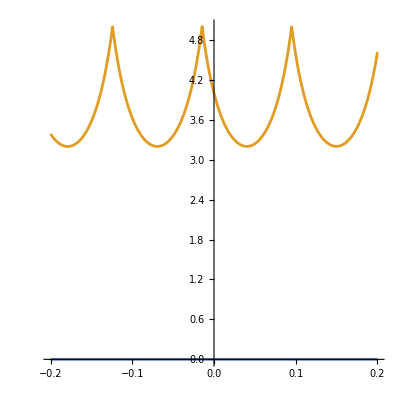

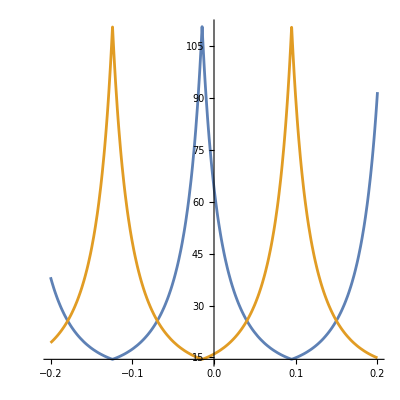

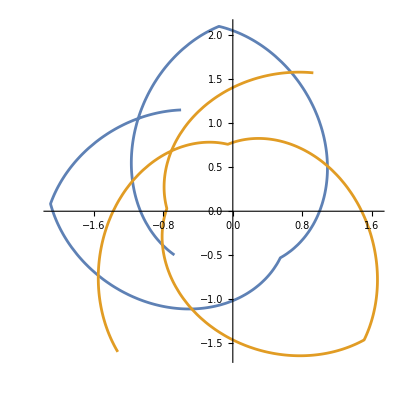

{{-2.10088,1.66727},{-1.63905,2.09631}}

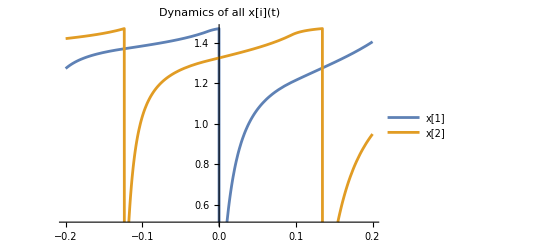

```mathematica
ClearAll["Global`*"];
(*Define the system of equations*)
L=10;  (*Threshold for wrap-around*)

Dist[a_,b_]:=Min[Abs[a-b],L-Abs[a-b]];
DistX[a_,b_]:=Sign[a-b]Sign[L/2-Abs[a-b]];
uF[xx_,t_]:=Apply[Plus,Table[m[j][t]Dist[xx,x[j][t]],{j,1,n}]]
u[k_,t_]:=Apply[Plus,Table[m[j][t]Dist[x[j][t],x[k][t]],{j,1,n}]]
ux[k_,t_]:=Apply[Plus,Table[-m[j][t]DistX[x[j][t],x[k][t]],{j,1,n}]]

n=2; 

initialConditions=Flatten[Table[{m[i][0]==RandomReal[{-10,10}],x[i][0]==RandomReal[{0,L}]},{i,n}]]
initialConditions={
m[1][0]==1,x[1][0]==0,
m[2][0]==-2,x[2][0]==4,
m[3][0]==-5,x[3][0]==2
};

(*Define the system of ODEs*)
eqns=Flatten[Table[{
m[i]'[t]==-m[i][t]ux[i,t]u[i,t],
x[i]'[t]==u[i,t]^2},
{i,n}
]];
(*Solve the system numerically*)
Tstart=-0.2;
Tend=0.2;
T={t,Tstart,Tend};
S=10^-3;
wrapEvents=Flatten[Table[
With[{i=i},
{
WhenEvent[x[i][t]>L+S,x[i][t]->0],
WhenEvent[x[i][t]<0-S,x[i][t]->L]
}],{i,n}
]];

sol=NDSolve[Join[eqns,initialConditions,wrapEvents],Flatten[Table[{m[i],x[i]},{i,n}]],T];

XD[i_,t_]=m[i][t];
Circ[a_,r_]:={r Cos[2Pi a /L],r Sin[2Pi a /L]};
Circ[a_,r_]:={r Cos[2Pi a /L],r Sin[2Pi a /L]};

M1=(m[1][0]^2+m[2][0]^2)/.sol[[1]];
M2=m[1][0]m[2][0]Dist[x[1][0],x[2][0]]/.sol[[1]];

FindPeakDistances[y_]:=Block[{yValues,peaks,tValues,peakTimes,peakDistances},
yValues=y[[All,2]];
peaks=FindPeaks[yValues];
tValues=y[[All,1]];
peakTimes=tValues[[peaks[[All,1]]]];
peakDistances=Differences[peakTimes];
{peakDistances}
]
FindPeakDistances[Table[{t,Mod[x[1][t]-x[2][t],L]/.sol[[1]]},{t,Tstart,Tend,0.001}]]
FindPeakDistances[Table[{t,Mod[m[1][t],L]/.sol[[1]]},{t,Tstart,Tend,0.001}]]
FindPeakDistances[Table[{t,Mod[m[2][t],L]/.sol[[1]]},{t,Tstart,Tend,0.001}]]

ModN[i_]:=Mod[i-1,n]+1;
color[x_]:=ColorData["Rainbow"][x];
test=Function[{x,y,z},color[Rescale[z,{-0.4,1.05}]]];
(*Plot3D[uF[x,t]/.sol[[1]],{x,0,10},{t,Tstart,Tend},PlotPoints->100,Boxed->False,ColorFunction->test]*)
ParametricPlot[Evaluate[Table[{t,x[i][t]}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[Table[{t,Mod[x[ModN[i]][t]-x[ModN[i+1]][t],L]}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,Mod[x[1][t]-x[2][t],L]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1];
ParametricPlot[Evaluate[Join[Table[{t,x[i][t]}/.sol[[1]],{i,n}],{
	{t,-(M2/M1)Cot[M2 t+Pi/4]+0.5},
	{t,+(M2/M1)Tan[M2 t+Pi/4]+0.5},
	{t,-(M2/M1)Cot[M2 (t-0.685)+ArcTan[10]]+10.5},
	{t,-(M2/M1)Cot[M2 (t-0.685)+0.5]}
}]
],{t,Tstart,Tend},AspectRatio->1,PlotRange->{Automatic,{0,10}}];

ParametricPlot[Evaluate[Table[{t,m[i][t]}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[Table[{t,Min[Abs[x[1][t]-x[i][t]],L-Abs[x[1][t]-x[i][t]]]}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[Table[{t,u[i,t]^2}/.sol[[1]],{i,n}]],{t,Tstart,Tend},AspectRatio->1]
pp=ParametricPlot[Evaluate[Table[Circ[x[i][t],XD[i,t]]/.sol[[1]],{i,n}]],{t,Tstart,Tend}]
plotRange1={{-1,1},{-1,1}};
plotRange1=AbsoluteOptions[pp,PlotRange][[1]][[2]]
Manipulate[Graphics[Point[Evaluate[Table[Circ[x[i][d],XD[i,d]]/.sol[[1]],{i,n}]]],Axes->True,PlotRange->plotRange1],{d,Tstart,Tend}]

plotX=Plot[Evaluate[Table[ArcTan[x[i][t]]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]
```

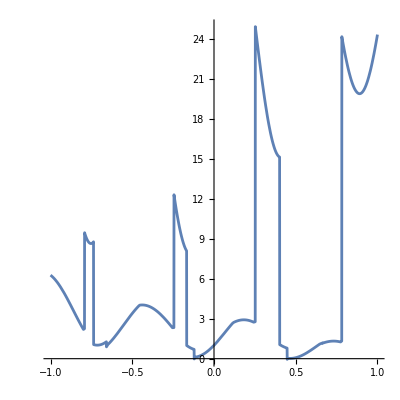

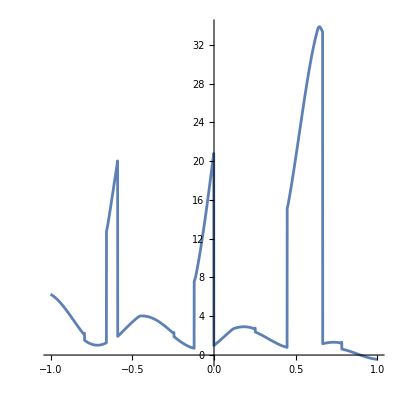

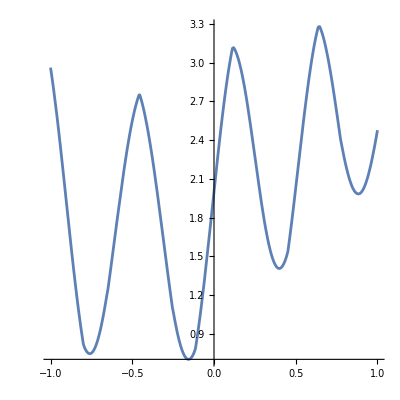

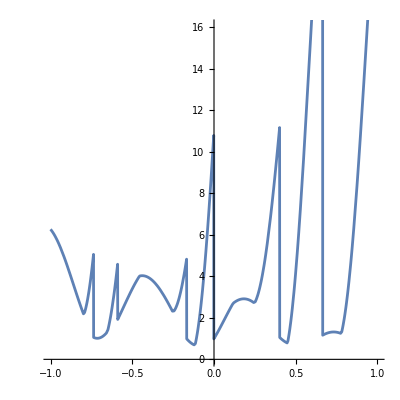

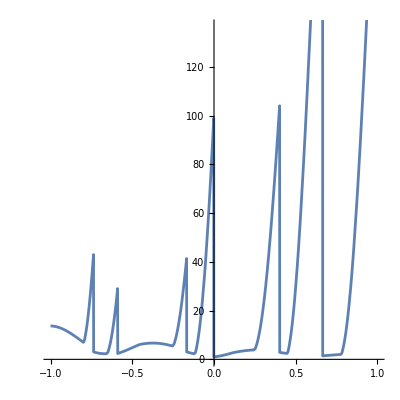

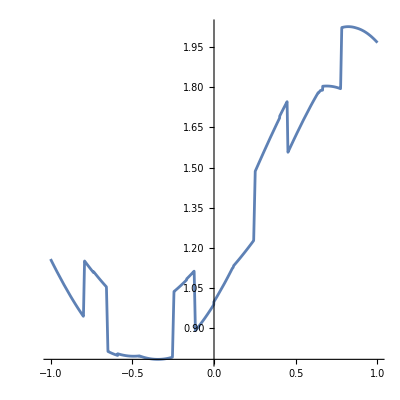

```mathematica
ParametricPlot[Evaluate[{t,x[2][t](m[1][t]^2+m[2][t]^2)-m[1][t]^2Dist[x[2][t],x[1][t]]DistX[x[2][t],x[1][t]]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,x[1][t](m[1][t]^2+m[2][t]^2)+m[2][t]^2Dist[x[2][t],x[1][t]]DistX[x[2][t],x[1][t]]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]

ParametricPlot[Evaluate[{t,m[1][t]^2x[1][t]^0+m[2][t]^2x[2][t]^0}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,m[1][t]^2x[1][t]^1+m[2][t]^2x[2][t]^1}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,m[1][t]^2x[1][t]^2+m[2][t]^2x[2][t]^2}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,m[1][t]m[2][t]Dist[x[2][t],x[1][t]]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
```

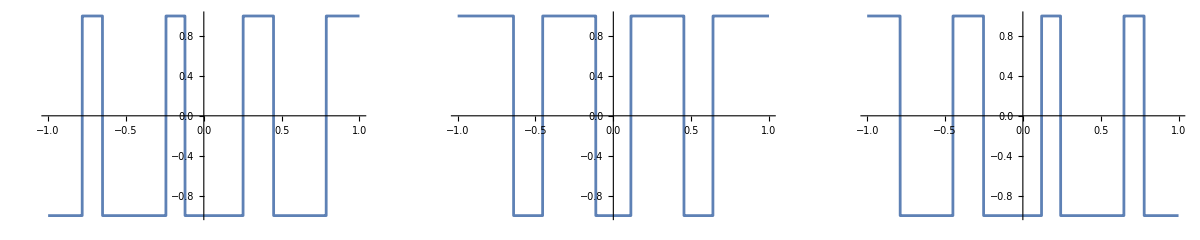

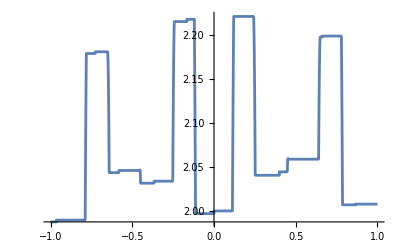

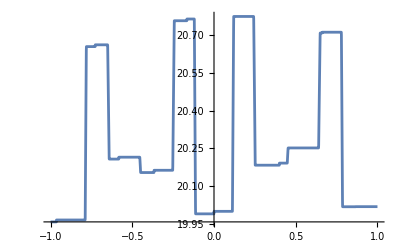

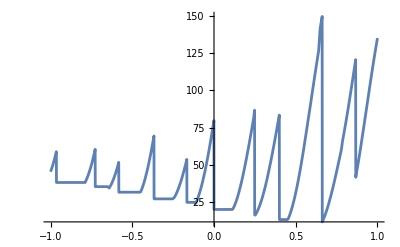

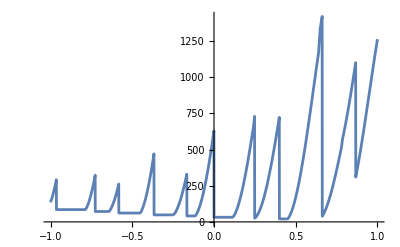

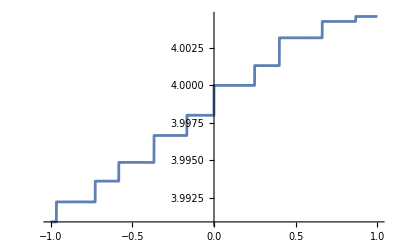

```mathematica
(*ParametricPlot[Evaluate[{t,x[2][t](m[1][t]^2+m[2][t]^2)-m[1][t]^2Dist[x[2][t],x[1][t]]DistX[x[2][t],x[1][t]]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]
ParametricPlot[Evaluate[{t,x[1][t](m[1][t]^2+m[2][t]^2)+m[2][t]^2Dist[x[2][t],x[1][t]]DistX[x[2][t],x[1][t]]}/.sol[[1]]],{t,Tstart,Tend},AspectRatio->1]*)

plot1=Plot[Evaluate[DistX[x[1][t],x[2][t]]/.sol[[1]]],T];
plot2=Plot[Evaluate[DistX[x[1][t],x[3][t]]/.sol[[1]]],T];
plot3=Plot[Evaluate[DistX[x[2][t],x[3][t]]/.sol[[1]]],T];
GraphicsRow[{plot1,plot2,plot3}]

M1=(m[1][t]m[2][t]Dist[x[2][t],x[1][t]]+m[1][t]m[3][t]Dist[x[3][t],x[1][t]]+m[2][t]m[3][t]Dist[x[3][t],x[2][t]])/.sol[[1]];
M2=(m[1][t]m[2][t]m[3][t])^2Dist[x[2][t],x[1][t]]Dist[x[3][t],x[1][t]]Dist[x[3][t],x[2][t]]/.sol[[1]];
A1=m[1][t]^2(M1+2m[2][t]m[3][t]Dist[x[3][t],x[2][t]]);
A2=m[2][t]^2(M1+2m[1][t]m[3][t]Dist[x[3][t],x[1][t]]);
A3=m[3][t]^2(M1+2m[1][t]m[2][t]Dist[x[2][t],x[1][t]]);
M3A=(A1 x[1][t]^0+A2 x[2][t]^0+A3 x[3][t]^0)/.sol[[1]];
M3B=(A1 x[1][t]^1+A2 x[2][t]^1+A3 x[3][t]^1)/.sol[[1]];
M3C=(A1 x[1][t]^2+A2 x[2][t]^2+A3 x[3][t]^2)/.sol[[1]];
plotX=Plot[Evaluate[M2],T]
plotX=Plot[Evaluate[M3A],T]
plotX=Plot[Evaluate[M3B],T]
plotX=Plot[Evaluate[M3C],T]
plotX=Plot[Evaluate[M1],T]
```